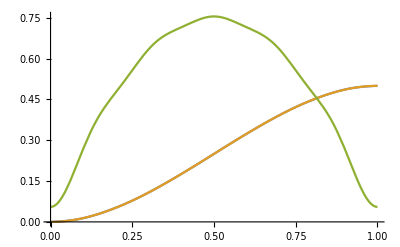

```mathematica
ClearAll["Global'*"];
(*harmonic basis*)
Subscript[ϕ, -1][x_]:=x;
Subscript[ϕ, 0][x_]:=1-x;
Subscript[ϕ, 1][x_]:=Sin[π x];
Subscript[ϕ, 2][x_]:=Sin[2π x];
Subscript[ϕ, 3][x_]:=Sin[3π x];
Subscript[ϕ, 4][x_]:=Sin[4π x];
Subscript[ϕ, 5][x_]:=Sin[5π x];
Subscript[ϕ, 6][x_]:=Sin[6π x];
Subscript[ϕ, 7][x_]:=Sin[7π x];
Subscript[ϕ, 8][x_]:=Sin[8π x];
Subscript[ϕ, 9][x_]:=Sin[9π x];
Subscript[ϕ, 10][x_]:=Sin[10π x];
Subscript[ϕ, 11][x_]:=Sin[11π x];
Subscript[ϕ, 12][x_]:=Sin[12π x];
(*stiff matrix for -Subscript[u, xx]+u=f*)
BasisN=12;(*or 2+6 2+12*)
StfMat=Table [Integrate[Subscript[ϕ, ii-2][x]*Subscript[ϕ, j-2][x]+D[Subscript[ϕ, ii-2][x],x]*D[Subscript[ϕ, j-2][x],x],{x,0,1}],{ii,BasisN},{j,BasisN}];
force[x_]:=-x^3+3/2 x^2+6 x-3;
ForceVec=Table[Integrate[force[x]*Subscript[ϕ, i-2][x],{x,0,1}],{i,BasisN}];
CoeffVec=LinearSolve[StfMat,ForceVec];
Solution[x_]:=(val=0;For[k=1,k≤BasisN,k++,val=val+CoeffVec[[k]]*Subscript[ϕ, k-2][x]];Return[val]);
PreciseSol[x_]:=-x^3+3/2 x^2;
DerivSol[x_]=D[Solution[x],x];
Plot[{Solution[x],PreciseSol[x],DerivSol[x]},{x,0,1}]
```

```mathematica
(*从这里可以看到，即使Galerkin解与准确解在H^1 范数下十分接近，其两端的导数值仍然不在0附近，且趋于0的速度极慢*)
```